```mathematica
(* nth multiple and non-multiple of arbitrary finite subsets of positive integers *)
```

```mathematica
bruh[n_,k_]:= Floor[(k*n-1)/(k-1)]
```

```mathematica
(* Test with k=4 *)
Table[bruh[n,4],{n,0,25}]
```

{-1,1,2,3,5,6,7,9,10,11,13,14,15,17,18,19,21,22,23,25,26,27,29,30,31,33}

```mathematica
bruh2[n_,k_]:= 1+n+Floor[n/(k-1)]
```

```mathematica
Table[bruh2[n, 4],{n,0,25}]
```

{1,2,3,5,6,7,9,10,11,13,14,15,17,18,19,21,22,23,25,26,27,29,30,31,33,34}

```mathematica
(* We're gonna use bruh2 from now on!!! I like it better, since it has  f[0] = 1 for any k, whereas  the other one has  f[0] = -1. *)
```

```mathematica
(* Okay... now let's do some numerical experimentation with the general case. *)
S={2,3,7}
multiples = {0,2,3,4,6,7,8,9,10,12,14,15,16,18,20,21,22,24,26,27,28,30,32,33,34,35,36,38,40,42}
nonmultiples = {1,5,11,13,17,19,23,25,29,31,37,39,41}
```

{2,3,7}

{0,2,3,4,6,7,8,9,10,12,14,15,16,18,20,21,22,24,26,27,28,30,32,33,34,35,36,38,40,42}

{1,5,11,13,17,19,23,25,29,31,37,39,41}

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42}

30

13

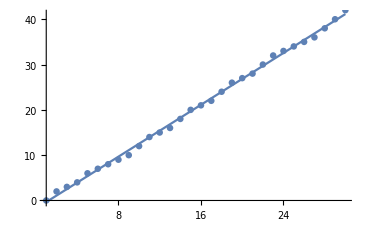

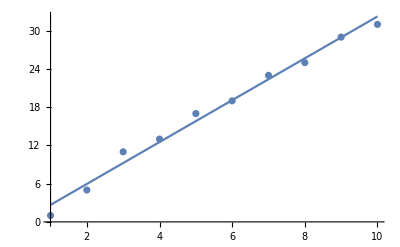

```mathematica
(* ... now what? *)
(* Get fits of each one. *)
f1=Fit[multiples,{1,x},x];
f2=Fit[nonmultiples,{1,x},x];
Show[Plot[{f1},{x,1,30}],ListPlot@multiples]
Show[Plot[{f2},{x,1,10}],ListPlot@nonmultiples]
```

```mathematica
f1
f2
```

-1.77241+1.43048 x

-0.615385+3.28571 x

```mathematica
(* Now, let's add them togetther!!*) 
sublistmults = {0,2,3,4,6,7,8,9,10,12,14,15,16}
result = sublistmults + nonmultiples
```

{0,2,3,4,6,7,8,9,10,12,14,15,16}

{1,7,14,17,23,26,31,34,39,43,51,54,57}

```mathematica
{6,7,3,6,3,5,3,5,4,8,3,3}
```